```mathematica
TrigToExp[Sinh[x]]
```

-ⅇ^-x/2+ⅇ^x/2

```mathematica
TrigToExp[Sin[x]]
```

1/2 ⅈ ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x)

```mathematica
% //TraditionalForm
```

-1/2 ⅈ ⅇ^(-ⅈ x) (-1+ⅇ^(2 ⅈ x))

```mathematica
Simplify[1/2 ⅈ ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x)]
```

-1/2 ⅈ ⅇ^(-ⅈ x) (-1+ⅇ^(2 ⅈ x))

```mathematica
ExpToTrig[1/2 ⅈ ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x)]
```

Sin[x]

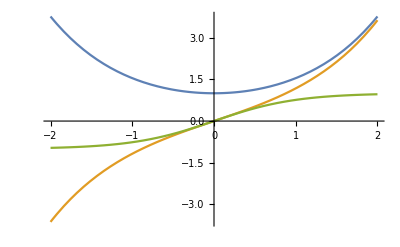

```mathematica
Plot[{Cosh[x],Sinh[x],Tanh[x]},{x,-2,2}]
```

```mathematica
ComplexPlot3D[Cosh[z],{z,-π/4-4I,π/4+4I},PlotLegends->Automatic]
```

-Graphics3D-

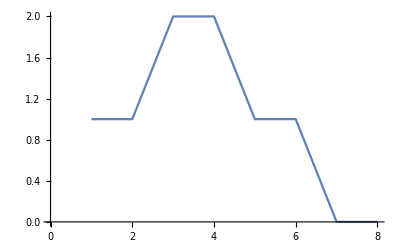

```mathematica
pts={1,1,2,2,1,1,0,0};
ListLinePlot[pts]
```

```mathematica
r=Fourier[pts]
```

{2.82843+0. ⅈ,-0.5+1.20711 ⅈ,0.+0. ⅈ,0.5-0.207107 ⅈ,0.+0. ⅈ,0.5+0.207107 ⅈ,0.+0. ⅈ,-0.5-1.20711 ⅈ}

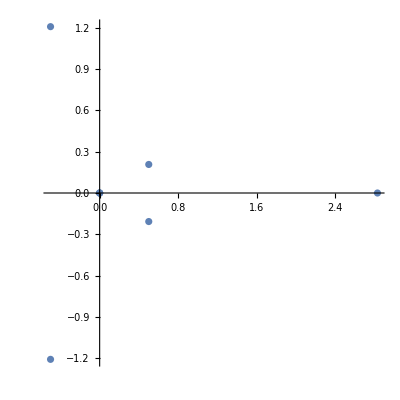

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@r,AspectRatio->1]
```

## 参考文档

https : // zhuanlan . zhihu . com/p/20042215